```mathematica
f[x_]:=(3 x+1) Mod[x,2]+(x/2) Mod[x+1,2]
```

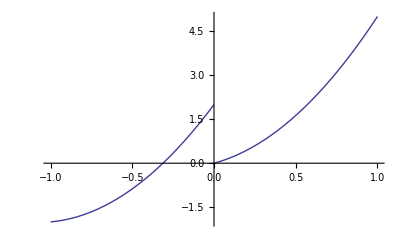

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
Manipulate[Plot[Nest[f,x,n],{x,0,100},PlotRange->{0,20}],{n,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[Nest[f,x,n],{x,1,10}]],{n,1,10,1}]
```